```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
```

# How Can We Fix the Electoral College?

### This is a two-step question: First, how should we allocate members of the House of Representatives (and many should there be?), and second, how should each state award its electoral votes in each Presidential election?

## Step One: Apportionment of House Seats

### Loading the data

While Mathematica has population conveniently built in to state entities, let’s be extra careful and use the same decennial Census figures the U.S. used for apportionment, as well as the official number of representatives per state allotted every tens years. This data is conveniently organized on Census.gov and gathered in `getPopulationApportionment.nb`

```mathematica
(* statePopulations = CloudGet["https://www.wolframcloud.com/objects/ad3e2c70-ebd6-42c0-b038-60f937486a84"]; *)
stateInfo = Import["./data/state_population_reps_evs.wl"];
stateInfo[LinguisticAssistant]
```

<|name→Pennsylvania,abbr→PA,entity→Pennsylvania, United States,population_decennial→<|1910→7665111,1920→8720017,1930→9631350,1940→9900180,1950→10498012,1960→11319366,1970→11793909,1980→11863895,1990→11881643,2000→12281054,2010→12702379|>,representatives→<|1910→36,1920→36,1930→34,1940→33,1950→30,1960→27,1970→25,1980→23,1990→21,2000→19,2010→18|>,evs→<|1910→38,1920→38,1930→36,1940→35,1950→32,1960→29,1970→27,1980→25,1990→23,2000→21,2010→20|>|>

We may need to access state info by state abbreviation as well

```mathematica
stateAbbrs = #["abbr"]& /@ Values@stateInfo;
statesByAbbreviation = AssociationThread[stateAbbrs, Values@stateInfo];
```

### The Huntington-Hill method

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the “method of equal proportions,” to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: it’s population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

["https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions"](https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions)

Let’s make this equation a function, using the state entity and an association of electoral votes as allotted so far.

```mathematica
PriorityHuntingtonHill[stateAbbr_, stateEVs_] := 1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / Sqrt[stateEVs * (stateEVs + 1)]
```

The allocation function will assign electoral votes according to the above formula one at a time, using population figures from the specified year. We’re also going to explicitly pass the priority function in case we want to try a different one later (which we definitely will). To save time, we’re also going to store the priorities until we update the number of seats in a state, rather than run 50 square roots 385 times.

```mathematica
AllocateOne[evs_, priorities_, print_:False, priorityFunc_:PriorityHuntingtonHill] := (
	newEVs = evs;
	newPriorities = priorities;

	topPriority = First[Keys[Reverse[Sort[priorities]]]];
	newEVs[topPriority] += 1;
	
	If[print, Print["Electoral vote number " <> ToString@Total@newEVs <> " goes to " <> topPriority <> " for a total of " <> ToString@newEVs[topPriority]]];
	newPriorities[topPriority] = priorityFunc[topPriority, newEVs[topPriority]];
	{ newEVs, newPriorities }
)
```

Let’s test it once, starting with one EV per state. California should get the first. We don’t want to include poor DC here since it has automatically received three electoral votes since 1961.

```mathematica
stateAbbrs50 = Select[stateAbbrs, # ≠ "DC"&];
```

```mathematica
stateEVs = AssociationThread[stateAbbrs50, ConstantArray[1, 50]];
statePriorities = AssociationThread[stateAbbrs50, PriorityHuntingtonHill[#, 1]& /@ stateAbbrs50];
AllocateOne[stateEVs, statePriorities, True];
```

Electoral vote number 51 goes to CA for a total of 2

Now let’s run it for all 50 states. We’re going to parameterize all aspects of the allocation algorithm:

The total number of seats to allocate (total_), defaulting to 435 (the number of members in the House)

The minimum number of seats each state gets (min_), defaulting to 1

The remaining number of seats each state gets (extra_), defaulting to 2 -- the number of senators per state

The priority function for allocation (priorityFunc_), defaulting to Huntington-Hill

```mathematica
calculateAllocations[total_:435, min_:1, extra_:2, priorityFunc_:PriorityHuntingtonHill]:= (
	stateEVs = AssociationThread[stateAbbrs50, ConstantArray[1, 50]];
	statePriorities = AssociationThread[stateAbbrs50, PriorityHuntingtonHill[#, 1]& /@ stateAbbrs50];
	remaining = total - 50 * min;
	While[Total@stateEVs < total, { stateEVs, statePriorities } = AllocateOne[stateEVs, statePriorities, False, priorityFunc]];
	(* Add extra to each state -- normally two for Senators *)
	stateEVs = AssociationThread[Keys@stateEVs, Values@stateEVs + extra];
	(* DC always gets the minimum *)	
	stateEVs["DC"] = min + extra;
	KeySort@stateEVs
)
```

```mathematica
results = calculateAllocations[];
{ results["AL"], results["KY"], results["DC"] }
```

{9,8,3}

### Let' s compare those results to the actual allocation

```mathematica
{ green = RGBColor["#47C045"], orange = RGBColor["#FFBC2D"], purple = RGBColor["#E165FA"] }
```

{RGBColor[0.2784313725490196, 0.7529411764705882, 0.27058823529411763],RGBColor[1., 0.7372549019607844, 0.17647058823529413],RGBColor[0.8823529411764706, 0.396078431372549, 0.9803921568627451]}

```mathematica
realEVs = KeySort@AssociationThread[stateAbbrs, Values[#["evs"]["2010"]& /@ stateInfo]];
```

```mathematica
compareAllocations[calculatedEVs_] := (
	diffs = calculatedEVs - realEVs;
	maxEV = Max[{Max[calculatedEVs], Max[realEVs]}];
	{ minDiff, maxDiff } = MinMax[diffs];	
	colorScales = <|
		"ev" -> Function[ev, Blend[Transpose[{{0, maxEV}, { White, purple }}], ev]],
		"diff" -> Function[d, Blend[Transpose[{{minDiff - 1, 0, maxDiff + 1}, { orange, White, green }}], d]]
	|>;

	cols = Column[
		{ #, realEVs[#], calculatedEVs[#], diffs[#] },
		Frame->All, Alignment->"Center", Spacings-> { 1, 0.8 }, ItemSize-> {If[#["calculated_evs"] ≥ 100, 2, 1], 1.4},
		Background->{
			White,
			colorScales["ev"][realEVs[#]],
			colorScales["ev"][calculatedEVs[#]],
			colorScales["diff"][diffs[#]]
		}
	]& /@ Keys@realEVs;
	
	cols = Prepend[cols, Column[{
		"State",
		"Real EVs",
		"New EVs",
		"Diff"
	}, Alignment->Right, Frame->All, Spacings-> { 1, 0.8 }, ItemSize-> {5, 1.4}]];

	cols = Append[cols, Column[
		{ 
			Style["Total", Bold],
			Total[realEVs],
			Total[calculatedEVs],
			Total[diffs]
		},
		Frame->All, Alignment->"Center", Spacings-> { 1, 0.8 }, ItemSize-> {3, 1.4},
		Background->{White, White, White, colorScales["diff"][Total[diffs]] }
	]];	
	
	cols = Map[
		Style[#, FontSize->9]&,
		cols
	];
	Grid[{cols}, Spacings->-0.1]
)
compareAllocations[results]
```

State
Real EVs
New EVs
Diff | AK
3
3
0 | AL
9
9
0 | AR
6
6
0 | AZ
11
11
0 | CA
55
55
0 | CO
9
9
0 | CT
7
7
0 | DC
3
3
0 | DE
3
3
0 | FL
29
29
0 | GA
16
16
0 | HI
4
4
0 | IA
6
6
0 | ID
4
4
0 | IL
20
20
0 | IN
11
11
0 | KS
6
6
0 | KY
8
8
0 | LA
8
8
0 | MA
11
11
0 | MD
10
10
0 | ME
4
4
0 | MI
16
16
0 | MN
10
10
0 | MO
10
10
0 | MS
6
6
0 | MT
3
3
0 | NC
15
15
0 | ND
3
3
0 | NE
5
5
0 | NH
4
4
0 | NJ
14
14
0 | NM
5
5
0 | NV
6
6
0 | NY
29
29
0 | OH
18
18
0 | OK
7
7
0 | OR
7
7
0 | PA
20
20
0 | RI
4
4
0 | SC
9
9
0 | SD
3
3
0 | TN
11
11
0 | TX
38
38
0 | UT
6
6
0 | VA
13
13
0 | VT
3
3
0 | WA
12
12
0 | WI
10
10
0 | WV
5
5
0 | WY
3
3
0 | Total
538
538
0

Our algorithm works! Now let’s see what happens when we change some of the parameters

Here’s what allocation would look like if there were 1,000 members of the House

```mathematica
bigHouse = calculateAllocations[1000];
compareAllocations[bigHouse]
```

State
Real EVs
New EVs
Diff | AK
3
4
1 | AL
9
18
9 | AR
6
11
5 | AZ
11
23
12 | CA
55
123
68 | CO
9
18
9 | CT
7
14
7 | DC
3
3
0 | DE
3
5
2 | FL
29
63
34 | GA
16
33
17 | HI
4
6
2 | IA
6
12
6 | ID
4
7
3 | IL
20
44
24 | IN
11
23
12 | KS
6
11
5 | KY
8
16
8 | LA
8
17
9 | MA
11
23
12 | MD
10
21
11 | ME
4
6
2 | MI
16
34
18 | MN
10
19
9 | MO
10
21
11 | MS
6
12
6 | MT
3
5
2 | NC
15
33
18 | ND
3
4
1 | NE
5
8
3 | NH
4
6
2 | NJ
14
31
17 | NM
5
9
4 | NV
6
11
5 | NY
29
65
36 | OH
18
40
22 | OK
7
14
7 | OR
7
14
7 | PA
20
43
23 | RI
4
5
1 | SC
9
17
8 | SD
3
5
2 | TN
11
23
12 | TX
38
84
46 | UT
6
11
5 | VA
13
28
15 | VT
3
4
1 | WA
12
24
12 | WI
10
20
10 | WV
5
8
3 | WY
3
4
1 | Total
538
1103
565

And here were are with the same 538 total electoral votes, but without the senators adding two to each state

```mathematica
noSenators = calculateAllocations[537, 1, 0];
compareAllocations[noSenators]
```

State
Real EVs
New EVs
Diff | AK
3
1
-2 | AL
9
8
-1 | AR
6
5
-1 | AZ
11
11
0 | CA
55
65
10 | CO
9
9
0 | CT
7
6
-1 | DC
3
1
-2 | DE
3
2
-1 | FL
29
33
4 | GA
16
17
1 | HI
4
2
-2 | IA
6
5
-1 | ID
4
3
-1 | IL
20
22
2 | IN
11
11
0 | KS
6
5
-1 | KY
8
8
0 | LA
8
8
0 | MA
11
11
0 | MD
10
10
0 | ME
4
2
-2 | MI
16
17
1 | MN
10
9
-1 | MO
10
10
0 | MS
6
5
-1 | MT
3
2
-1 | NC
15
17
2 | ND
3
1
-2 | NE
5
3
-2 | NH
4
2
-2 | NJ
14
15
1 | NM
5
4
-1 | NV
6
5
-1 | NY
29
34
5 | OH
18
20
2 | OK
7
7
0 | OR
7
7
0 | PA
20
22
2 | RI
4
2
-2 | SC
9
8
-1 | SD
3
2
-1 | TN
11
11
0 | TX
38
44
6 | UT
6
5
-1 | VA
13
14
1 | VT
3
1
-2 | WA
12
12
0 | WI
10
10
0 | WV
5
3
-2 | WY
3
1
-2 | Total
538
538
0

And here’s a slightly cruder allocation algorithm that simply awards the next seat to the state with the most number of people per representative.

```mathematica
PriorityPerCapita[stateAbbr_, stateEVs_] := 1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / stateEVs;
simpleAlgo = calculateAllocations[435, 1, 2, PriorityPerCapita];
compareAllocations[simpleAlgo]
```

State
Real EVs
New EVs
Diff | AK
3
3
0 | AL
9
9
0 | AR
6
6
0 | AZ
11
11
0 | CA
55
53
-2 | CO
9
9
0 | CT
7
7
0 | DC
3
3
0 | DE
3
3
0 | FL
29
28
-1 | GA
16
16
0 | HI
4
4
0 | IA
6
7
1 | ID
4
5
1 | IL
20
20
0 | IN
11
11
0 | KS
6
6
0 | KY
8
8
0 | LA
8
9
1 | MA
11
11
0 | MD
10
10
0 | ME
4
4
0 | MI
16
16
0 | MN
10
10
0 | MO
10
11
1 | MS
6
6
0 | MT
3
3
0 | NC
15
15
0 | ND
3
3
0 | NE
5
5
0 | NH
4
4
0 | NJ
14
14
0 | NM
5
5
0 | NV
6
6
0 | NY
29
29
0 | OH
18
18
0 | OK
7
8
1 | OR
7
8
1 | PA
20
20
0 | RI
4
3
-1 | SC
9
9
0 | SD
3
3
0 | TN
11
11
0 | TX
38
36
-2 | UT
6
6
0 | VA
13
13
0 | VT
3
3
0 | WA
12
12
0 | WI
10
10
0 | WV
5
5
0 | WY
3
3
0 | Total
538
538
0

We' ll get fancier with our priority algos in a minute. But first ...

## Step Two : Awarding Electoral Votes

### Loading the Data

Election results are culled from fec.gov in `getElectionResultsFEC.nb`

```mathematica
(* electionResults = CloudGet["https://www.wolframcloud.com/objects/29199ad6-f71e-407f-9d19-6a15cdbe34dc"] *)
electionResults = Import["./data/election_results_2016.wl"];
electionsByAbbreviation = AssociationThread[stateAbbrs, Values@electionResults];
electionsByAbbreviation["ME"]
```

<|name→Maine,abbr→ME,entity→Maine, United States,ev_total→4,ev_trump→1.,ev_clinton→3.,votes_trump→335593.,votes_clinton→357735.,votes_others→54599.,votes_total→747927.,winner→<|name→Hillary Clinton,party→D|>|>

As it stands, all states and Washington, D.C. award their electoral votes in a winner-take-all fashion, with two exceptions: Nebraska and Maine split the electoral votes corresponding to their members of the House -- three and two electors, respectively -- according to the winner of each Congressional district. As you see above, in 2016 Donald Trump won one electoral vote in Maine while Clinton carried the other three.

Let’s make a function that allocates EVs according to the state election results, leaving the number of electoral votes parameterized since we’re fussing with allocation algorithms. In keeping with 2016 results, we’ll start by giving Trump 25 percent of Maine’s electoral votes, rounded down. We’ll try other functions in a sec.

```mathematica
electionWinner[stateAbbr_, stateEVs_:-1] := (
	results = electionsByAbbreviation[stateAbbr];
	EVs = If[stateEVs == -1, realEVs[stateAbbr], stateEVs];
	partial = If[stateAbbr == "ME", Floor[EVs / 4.0], 0];
	EVs = EVs - partial;		
	Dem = If[results["votes_trump"] > results["votes_clinton"], partial, EVs];
	Rep = If[results["votes_trump"] < results["votes_clinton"], partial, EVs];
	<| "state" -> stateAbbr, "evs" -> EVs + partial, "R" -> Rep, "D" -> Dem |>
)
electionWinner["ME", 8]
```

<|state→ME,evs→8,R→2,D→6|>

Okay, let’s run an election, starting with a rerun of 2016

```mathematica
runElection[allocation_:realEVs, winnerFunction_:electionWinner] := (
	states = winnerFunction[#, allocation[#]]& /@ Keys@allocation;
	totalD = Total[#["D"]& /@ states];
	totalR = Total[#["R"]& /@ states];
	<| "result" -> <| "R" -> totalR, "D" -> totalD, "Total" -> (totalD + totalR) |>, "states" -> AssociationThread[Keys@allocation, states] |>
)
rerun = runElection[];
rerun["result"]
```

<|R→306,D→232,Total→538|>

This tracks with reality exactly after accounting for “faithless electors,” who cast rogue ballots in the Electoral College.

["https://en.wikipedia.org/wiki/United_States_presidential_election,_2016#cite_note-pledged-2"](https://en.wikipedia.org/wiki/United_States_presidential_election,_2016#cite_note-pledged-2)

```mathematica
{ blue = RGBColor["#00B2FF"], red = RGBColor["#F15C53"] }
```

{RGBColor[0., 0.6980392156862745, 1.],RGBColor[0.9450980392156862, 0.3607843137254902, 0.3254901960784314]}

```mathematica
chartElection[electionResults_] := (
	evsR = #["R"]& /@ electionResults["states"];
	evsD = #["D"]& /@ electionResults["states"];
	evsTotal = #["evs"]& /@ electionResults["states"];
	max = Max[Max@votesR, Max@votesD];
	
	colorScales = <|   		
		"D" -> Function[ev, Blend[Transpose[{{0, max}, { White, blue }}], ev]],
		"R" -> Function[ev, Blend[Transpose[{{0, max}, { White, red }}], ev]]
	|>;

	cols = Column[{ #, evsD[#], evsR[#], evsTotal[#] },
		Frame->All, Alignment->"Center", Spacings -> { 1, 0.8 }, ItemSize -> { If[evsTotal[#] > 100, 2, 1.2], 1.4},
		Background->{
			White,
			colorScales["D"][evsD[#]],
			colorScales["R"][evsR[#]],
			White
		}		
	]& /@ Keys@electionResults["states"];
			
	cols = Prepend[cols, Column[{
		"State",
		"Clinton",
		"Trump",
		"Total"
	}, Alignment->Right, Frame->All, Spacings-> { 2, 0.8 }, ItemSize-> {4, 1.4}]];

	cols = Append[cols, Column[{ 
		Style["Total", Bold],
		Style[electionResults["result"]["D"], If[electionResults["result"]["D"] > electionResults["result"]["R"], Bold, Plain]],
		Style[electionResults["result"]["R"], If[electionResults["result"]["D"] > electionResults["result"]["R"], Plain, Bold]],
		electionResults["result"]["Total"]
	}, Frame->All, Alignment->"Center", Spacings-> { 1, 0.8 }, ItemSize-> {3, 1.4}, Background -> {
		White,
		If[electionResults["result"]["D"] > electionResults["result"]["R"], Yellow, White],
		If[electionResults["result"]["D"] > electionResults["result"]["R"], White, Yellow],
		White
	}
	]];
	
	cols = Map[
		Style[#, FontSize->9]&,
		cols
	];
	Grid[{cols}, Spacings->-0.1]
)
chartElection[rerun]
```

State
Clinton
Trump
Total | AK
0
3
3 | AL
0
9
9 | AR
0
6
6 | AZ
0
11
11 | CA
55
0
55 | CO
9
0
9 | CT
7
0
7 | DC
3
0
3 | DE
3
0
3 | FL
0
29
29 | GA
0
16
16 | HI
4
0
4 | IA
0
6
6 | ID
0
4
4 | IL
20
0
20 | IN
0
11
11 | KS
0
6
6 | KY
0
8
8 | LA
0
8
8 | MA
11
0
11 | MD
10
0
10 | ME
3
1
4 | MI
0
16
16 | MN
10
0
10 | MO
0
10
10 | MS
0
6
6 | MT
0
3
3 | NC
0
15
15 | ND
0
3
3 | NE
0
5
5 | NH
4
0
4 | NJ
14
0
14 | NM
5
0
5 | NV
6
0
6 | NY
29
0
29 | OH
0
18
18 | OK
0
7
7 | OR
7
0
7 | PA
0
20
20 | RI
4
0
4 | SC
0
9
9 | SD
0
3
3 | TN
0
11
11 | TX
0
38
38 | UT
0
6
6 | VA
13
0
13 | VT
3
0
3 | WA
12
0
12 | WI
0
10
10 | WV
0
5
5 | WY
0
3
3 | Total
232
306
538

Let’s see what happens with one of those alternate apportionment algorithms

```mathematica
bigHouseElection = runElection[bigHouse];
bigHouseElection["result"]
chartElection[bigHouseElection]
```

<|R→625,D→478,Total→1103|>

State
Clinton
Trump
Total | AK
0
4
4 | AL
0
18
18 | AR
0
11
11 | AZ
0
23
23 | CA
123
0
123 | CO
18
0
18 | CT
14
0
14 | DC
3
0
3 | DE
5
0
5 | FL
0
63
63 | GA
0
33
33 | HI
6
0
6 | IA
0
12
12 | ID
0
7
7 | IL
44
0
44 | IN
0
23
23 | KS
0
11
11 | KY
0
16
16 | LA
0
17
17 | MA
23
0
23 | MD
21
0
21 | ME
5
1
6 | MI
0
34
34 | MN
19
0
19 | MO
0
21
21 | MS
0
12
12 | MT
0
5
5 | NC
0
33
33 | ND
0
4
4 | NE
0
8
8 | NH
6
0
6 | NJ
31
0
31 | NM
9
0
9 | NV
11
0
11 | NY
65
0
65 | OH
0
40
40 | OK
0
14
14 | OR
14
0
14 | PA
0
43
43 | RI
5
0
5 | SC
0
17
17 | SD
0
5
5 | TN
0
23
23 | TX
0
84
84 | UT
0
11
11 | VA
28
0
28 | VT
4
0
4 | WA
24
0
24 | WI
0
20
20 | WV
0
8
8 | WY
0
4
4 | Total
478
625
1103

And here’s the usual allocation, but with a different electoral algorithm that gives electors proportionally to the vote

```mathematica
electionProportional[stateAbbr_, stateEVs_:-1] := (
	EVs = If[stateEVs == -1, realEVs[stateAbbr], stateEVs];
	results = electionsByAbbreviation[stateAbbr];
	total = results["votes_trump"] + results["votes_clinton"];
	shareD = Round[EVs * results["votes_clinton"] / total];
	shareR = Round[EVs * results["votes_trump"] / total];
	Dem = If[results["votes_trump"] > results["votes_clinton"], EVs - shareR, shareD];
	Rep = If[results["votes_trump"] > results["votes_clinton"], shareR, EVs - shareD];
	<| "state" -> stateAbbr, "evs" -> EVs + partial, "R" -> Rep, "D" -> Dem |>
)
electionProportional["CA"]
```

<|state→CA,evs→55,R→19,D→36|>

```mathematica
proportional = runElection[realEVs, electionProportional];
proportional["result"]
chartElection[proportional]
```

<|R→268,D→270,Total→538|>

State
Clinton
Trump
Total | AK
1
2
3 | AL
3
6
9 | AR
2
4
6 | AZ
5
6
11 | CA
36
19
55 | CO
5
4
9 | CT
4
3
7 | DC
3
0
3 | DE
2
1
3 | FL
14
15
29 | GA
8
8
16 | HI
3
1
4 | IA
3
3
6 | ID
1
3
4 | IL
12
8
20 | IN
4
7
11 | KS
2
4
6 | KY
3
5
8 | LA
3
5
8 | MA
7
4
11 | MD
6
4
10 | ME
2
2
4 | MI
8
8
16 | MN
5
5
10 | MO
4
6
10 | MS
2
4
6 | MT
1
2
3 | NC
7
8
15 | ND
1
2
3 | NE
2
3
5 | NH
2
2
4 | NJ
8
6
14 | NM
3
2
5 | NV
3
3
6 | NY
18
11
29 | OH
8
10
18 | OK
2
5
7 | OR
4
3
7 | PA
10
10
20 | RI
2
2
4 | SC
4
5
9 | SD
1
2
3 | TN
4
7
11 | TX
17
21
38 | UT
2
4
6 | VA
7
6
13 | VT
2
1
3 | WA
7
5
12 | WI
5
5
10 | WV
1
4
5 | WY
1
2
3 | Total
270
268
538

And if we were to run a proportional election on a big House of Representatives?

```mathematica
bigProp = runElection[bigHouse, electionProportional];
bigProp["result"]
chartElection[bigProp]
```

<|R→544,D→559,Total→1103|>

State
Clinton
Trump
Total | AK
2
2
4 | AL
6
12
18 | AR
4
7
11 | AZ
11
12
23 | CA
81
42
123 | CO
9
9
18 | CT
8
6
14 | DC
3
0
3 | DE
3
2
5 | FL
31
32
63 | GA
16
17
33 | HI
4
2
6 | IA
5
7
12 | ID
2
5
7 | IL
26
18
44 | IN
9
14
23 | KS
4
7
11 | KY
5
11
16 | LA
7
10
17 | MA
15
8
23 | MD
13
8
21 | ME
3
3
6 | MI
17
17
34 | MN
10
9
19 | MO
8
13
21 | MS
5
7
12 | MT
2
3
5 | NC
16
17
33 | ND
1
3
4 | NE
3
5
8 | NH
3
3
6 | NJ
18
13
31 | NM
5
4
9 | NV
6
5
11 | NY
40
25
65 | OH
18
22
40 | OK
4
10
14 | OR
8
6
14 | PA
21
22
43 | RI
3
2
5 | SC
7
10
17 | SD
2
3
5 | TN
8
15
23 | TX
38
46
84 | UT
4
7
11 | VA
15
13
28 | VT
3
1
4 | WA
14
10
24 | WI
10
10
20 | WV
2
6
8 | WY
1
3
4 | Total
559
544
1103

### Mapping the results

```mathematica
entityMap = AssociationThread[Keys@rerun["states"], Interpreter["USState"][#]& /@ Keys@rerun["states"]];
```

```mathematica
imageTrump = ImageCrop[Entity["Person","DonaldTrump::6vv3q"]["Image"], { 75, 75 }, Bottom];
imageClinton = ImageCrop[Entity["Person","HillaryClinton::538v8"]["Image"], { 75, 75 }, {0, -0.6}];
```

```mathematica
resultBox[result_] := (
	colorTrump = If[result["D"] < result["R"], LightYellow, White];
	colorClinton = If[result["D"] < result["R"], White, LightYellow];
	Row[{
		Column[{ Style["Donald Trump", FontSize->12], imageTrump, Style[result["R"], FontSize->16, Bold] }, Frame -> True, Alignment->Center, Spacings-> { 3, 0.5 }, Background->colorTrump],
		Column[{}, Frame -> False, ItemSize->{2, 0}],
		Column[{ Style["Hillary Clinton", FontSize->12], imageClinton, Style[result["D"], FontSize->16, Bold] }, Frame -> True, Alignment->Center, Spacings-> { 3, 0.5 }, Background->colorClinton ]
	}, ImageSize->480, Alignment->Center]
)
```

```mathematica
mapElection[electionResults_] := (
	(* We need the election results as a List of Entity -> result *)
	margins = #["D"] - #["R"]& /@ electionResults["states"];
	dataPolitical = entityMap[#] -> margins[#]& /@ Keys@margins;
	dataEVs = entityMap[#] -> electionResults["states"][#]["evs"]& /@ Keys@margins;

	maxMargin = Round[0.8 * Max[Abs /@ margins]];
	maxEV = Max[#["evs"] & /@ electionResults["states"]];
		
	colorsPolitics = { "ThermometerColors", "Reverse" };
	colorsEVs = { "GrayYellowTones", "Reverse" };
	
	schemePolitics = ColorData[colorsPolitics];
	schemeEVs = ColorData[colorsEVs];
	
	legendPolitics = BarLegend[{{ "ThermometerColors", "Reverse" }, {-maxMargin, maxMargin}}, LegendMarkerSize->400];
	legendEVs = BarLegend[{colorsEVs, {0, maxEV}}, LegendMarkerSize->400];
	
	contentinal = GeoRegionValuePlot[dataPolitical, GeoRange->Entity["Country","UnitedStates"], ImageSize->480, PlotLegends->None, ColorFunction->schemePolitics];
	ak = GeoRegionValuePlot[dataPolitical, GeoRange->Entity["AdministrativeDivision",{"Alaska","UnitedStates"}], GeoRangePadding -> {Scaled[0], None}, ImageSize->240, PlotLegends->None, ColorFunction->schemePolitics];
	hi = GeoRegionValuePlot[dataPolitical, GeoRange->Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}], GeoRangePadding -> {Scaled[0], None}, ImagePadding->{{10,0},{0,0}}, GeoRangePadding -> {Scaled[0], None}, ImageSize->240, PlotLegends->None, ColorFunction->schemePolitics];
	Column[{
		resultBox[electionResults["result"]],
		Row[{
			Column[{
				Row[{ contentinal }, ImageSize->480],
				Row[{ak,hi}, ImageSize->500]
			}],
			legendPolitics
		}]
	}]

)
mapElection[rerun]
```

Donald Trump
-Graphics-
306Hillary Clinton
-Graphics-
232
-Graphics-
-Graphics--Graphics-

## Okay, time to put them together!

There are lots of ways we can manipulate the results that do not require a Constitutional Amendment. Let’s start by looking at what happens with many different sizes of the House.

```mathematica
houseSizes = Table[calculateAllocations[x], {x, 100, 2000, 5 }];
houseSizesAssociation = AssociationThread[Table[ToString@x, {x, 100, 2000, 5 }], houseSizes];
```

```mathematica
electionSizes = runElection[#]& /@ Values@houseSizesAssociation;
electionSizesAssociation = AssociationThread[Table[ToString@x, {x, 100, 2000, 5 }], electionSizes];
```

Interestingly, the size of the House alone appears to have no bearing on the outcome

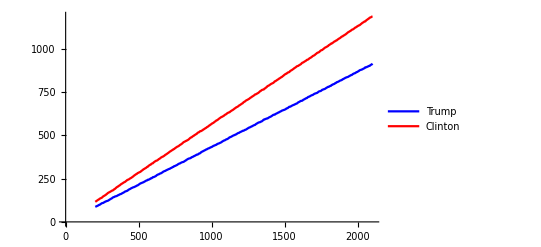

```mathematica
sizeTest = Values@#["result"]& /@ electionSizes;
{Rs, Ds, evs } = Transpose[sizeTest];
ListLinePlot[{Transpose[{evs, Ds}], Transpose[{evs, Rs}]}, PlotStyle->{Blue, Red}, PlotLegends->Placed[{"Trump", "Clinton"}, Above]]
```

```mathematica
l = Table[x, {x, 1, 53}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

```mathematica
Take[l, 27]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27}

```mathematica
Take[l, {28,Length@l}]
```

{28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}